FittedModel[0.8+0.4 x]

0.8+0.4 x

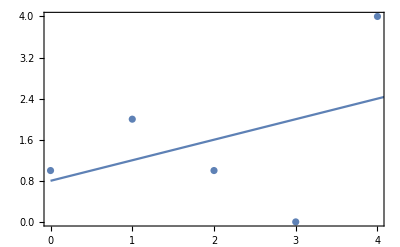

{0.2,0.8,-0.6,-2.,1.6}

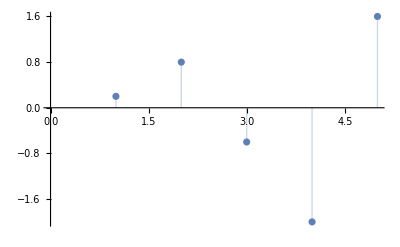

```mathematica
data={{0,1},{1,2},{2,1},{3,0},{4,4}};
lm=LinearModelFit[data,x,x]
Normal [lm]
Show[ListPlot[data],Plot[lm[x],{x,0,5}],Frame->True]
lm["FitResiduals"]
ListPlot[lm["FitResiduals"], Filling->Axis]
```

```mathematica
nlm=NonlinearModelFit[data,a0+a1 x+a2 x^2,{a0,a1,a2},x]
Normal[%]
Rationalize[%]
```

FittedModel[1.65714-«19» x+«20» x^2]

1.65714-1.31429 x+0.428571 x^2

58/35-(46 x)/35+(3 x^2)/7

```mathematica
(* Метод на най-малките квадрати *)
```

```mathematica
(* Задача 1 *)
```

Решава се системата:(6 | 3
3 | 19).(a_0
a_1) = (35
35)

Полиномът от първа степен е: 16/3+t

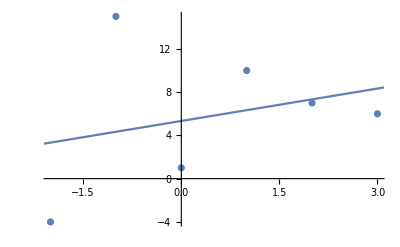

Абсолютна грешка: 14.3295

```mathematica
Clear[x,y,t,A,b]
(*x={0,1,2,3,4};
y={1,2,1,0,4};*)
x={-2,-1,0,1,2,3};
y={-4,15,1,10,7,6};
(*x={1.1,1.2,1.3,1.4,1.5};
y={4.23,4.52,4.87,5.28,5.75};*)
n=Length[x];
A=({{n, ∑_(i=1)^n x_⟦i⟧}, {∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2}});
 b={∑_(i=1)^n y_⟦i⟧,∑_(i=1)^n x_⟦i⟧*y_⟦i⟧};
Print["Решава се системата:",MatrixForm[A],".(a_0
a_1) = ",MatrixForm[b]]
s=LinearSolve[A,b];k=Length[s];
P[t_]:=s[[1]]+∑_(i=2)^k s[[i]]*t^(i-1);
Print["Полиномът от :043f:044a:0440:0432:0430 степен е: ",P[t]]
sp=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
g1=ListPlot[sp];
g2=Plot[P[t],{t,-5,5}];
Show[g1,g2]
Print["Абсолютна грешка: ",√(∑_(i=1)^n (P[x[[i]]]-y[[i]])^2)//N]
```

```mathematica
Clear[x,y,t,A,b]
(*x={0,1,2,3,4};
y={1,2,1,0,4};*)
x={-2,-1,0,1,2,3};
y={-4,15,1,10,7,6};
(*x={1.1,1.2,1.3,1.4,1.5};
y={4.23,4.52,4.87,5.28,5.75};*)
n=Length[x];
A=({{n, ∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2}, {∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2, ∑_(i=1)^n x_⟦i⟧^3}, {∑_(i=1)^n x_⟦i⟧^2, ∑_(i=1)^n x_⟦i⟧^3, ∑_(i=1)^n x_⟦i⟧^4}});
 b={∑_(i=1)^n y_⟦i⟧,∑_(i=1)^n x_⟦i⟧*y_⟦i⟧,∑_(i=1)^n x_⟦i⟧^2*y_⟦i⟧};
Print["Решава се системата:",MatrixForm[A],".(a_0
a_1
a_2) = ",MatrixForm[b]]
s=LinearSolve[A,b];k=Length[s];
P[t_]:=s[[1]]+∑_(i=2)^k s[[i]]*t^(i-1)
Print["Полиномът от :0432:0442:043e:0440:0430 степен е: ",P[t]]
sp=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
g1=ListPlot[sp];
g2=Plot[P[t],{t,-5,5}];
Show[g1,g2]
Print["Абсолютна грешка: ",√(∑_(i=1)^n (P[x[[i]]]-y[[i]])^2)//N]
```

```mathematica
(* Задача 4 *)
```

Стойностите на x са: {-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

Стойностите на y са: {-2.,-1.60902,-0.909017,-0.090983,0.609017,1.,1.00902,0.709017,0.290983,-0.00901699,0.}

Решава се системата:(11 | 6.66134×10^-16
6.66134×10^-16 | 4.4).(a_0
a_1) = (-1.
4.4)

Полиномът от първа степен е: -0.0909091+1. t

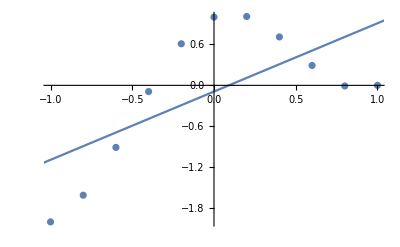

Абсолютна грешка: 2.43086

```mathematica
Clear[P,a0,a1,a2,t];
f[x_]:=Cos[π*x]+x; h=0.2;  (* дефинираме функцията *)
x=Table[x,{x,-1,1,h}];
y=Table[f[x], {x,-1, 1,h}];
Print["Стойностите на x са: ",x]
Print["Стойностите на y са: ",y]
n=Length[x];
A=({{n, ∑_(i=1)^n x_⟦i⟧}, {∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2}});
 b={∑_(i=1)^n y_⟦i⟧,∑_(i=1)^n x_⟦i⟧*y_⟦i⟧};
Print["Решава се системата:",MatrixForm[A],".(a_0
a_1) = ",MatrixForm[b]]
s=LinearSolve[A,b];k=Length[s];
P[t_]:=s[[1]]+∑_(i=2)^k s[[i]]*t^(i-1)
Print["Полиномът от :043f:044a:0440:0432:0430 степен е: ",P[t]]
sp=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
g1=ListPlot[sp];
g2=Plot[P[t],{t,-5,5}];
Show[g1,g2]
Print["Абсолютна грешка: ",√(∑_(i=1)^n (P[x[[i]]]-y[[i]])^2)//N]
```

Стойностите на x са: {-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

Стойностите на y са: {-2.,-1.60902,-0.909017,-0.090983,0.609017,1.,1.00902,0.709017,0.290983,-0.00901699,0.}

Решава се системата:(11 | 6.66134×10^-16 | 4.4
6.66134×10^-16 | 4.4 | 1.11022×10^-16
4.4 | 1.11022×10^-16 | 3.1328).(a_0
a_1
a_2) = (-1.
4.4
-3.09443)

Полиномът от втора степен е: 0.69418+1. t-1.96272 t^2

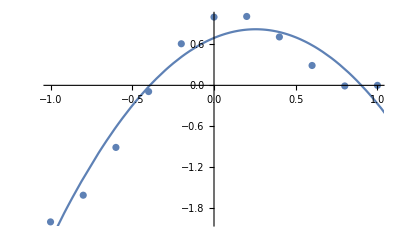

Абсолютна грешка: 0.787829

```mathematica
Clear[P,a0,a1,a2,t];
f[x_]:=Cos[π*x]+x; h=0.2;  (* дефинираме функцията *)
x=Table[x,{x,-1,1,h}];
y=Table[f[x],{x,-1, 1,h}];
Print["Стойностите на x са: ",x];
Print["Стойностите на y са: ",y];
n=Length[x];
A=({{n, ∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2}, {∑_(i=1)^n x_⟦i⟧, ∑_(i=1)^n x_⟦i⟧^2, ∑_(i=1)^n x_⟦i⟧^3}, {∑_(i=1)^n x_⟦i⟧^2, ∑_(i=1)^n x_⟦i⟧^3, ∑_(i=1)^n x_⟦i⟧^4}});
 b={∑_(i=1)^n y_⟦i⟧,∑_(i=1)^n x_⟦i⟧*y_⟦i⟧,∑_(i=1)^n x_⟦i⟧^2*y_⟦i⟧};
Print["Решава се системата:",MatrixForm[A],".(a_0
a_1
a_2) = ",MatrixForm[b]]
s=LinearSolve[A,b];k=Length[s];
P[t_]:=s[[1]]+∑_(i=2)^k s[[i]]*t^(i-1)
Print["Полиномът от :0432:0442:043e:0440:0430 степен е: ",P[t]]
sp=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
g1=ListPlot[sp];
g2=Plot[P[t],{t,-5,5}];
Show[g1,g2]
Table[(P[x[[i]]]-y[[i]])^2,{i,1,n}];
Print["Абсолютна грешка: ",√(∑_(i=1)^n (P[x[[i]]]-y[[i]])^2)//N]
```